# Night 6

### Clearing Variables

```mathematica
Clear["Global`*"]
```

### Defining Variables

```mathematica
f = (1/8)*x^2;
density =0.189;
ballastmass = 1000.;
xmin1 = -8.;
xmax1 = 8;
ymin1 = 0.;
ymax1 = 8.;
zmin1 = 0.;
zmax1 =26.;
xballast = 0.;
yballast = 2.;
xmast = 0.;
ymast = 26.;
mastmass = (177/4);
θ = 95.;
```

### Calculating Mass and Center of Mass

```mathematica
MassFunc[f_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,ballastmass_,xballast_,yballast_,density_,xmast_, ymast_,mastmass_]:=Module[{},
boat = ImplicitRegion[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}];

boatmass = zmax1*Integrate[density,{x, y}∈boat];

totalmass = boatmass+ballastmass;

xcomboat = ( 1/boatmass)*zmax1*Integrate[x*density,{x, y}∈boat];

ycomboat=N[( 1/boatmass)*zmax1*Integrate[y*density,{x, y}∈boat]];

xcom = 1/(totalmass)*(xcomboat*boatmass+xballast*ballastmass);

ycom = 1/(totalmass)*(ycomboat*boatmass+yballast*ballastmass+ymast*mastmass);

com = {xcom,ycom,0};

{boat,com, totalmass}
]
```

```mathematica
MassFunc[f,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,ballastmass,xballast,yballast,density,xmast, ymast,mastmass]
```

{ImplicitRegion[x^2/8<y<8.&&-8.<x<8&&0.<y<8.,{x,y}],{0.,3.63783,0},1419.33}

### Function/Module

```mathematica
Salmon[f_,density_,ballastmass_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,xballast_,yballast_,θ_, boat_, com_] := Module[{}, 
water = ImplicitRegion[If[θ<90, y<Tan[θ Degree]*x+d, y>Tan[θ Degree]*x+d],{{x,-8,8},{y,-8,8}}];

submerged = RegionIntersection[boat, water];

displacement = 1*zmax1*RegionMeasure[submerged];

draft = N[d/.FindRoot[displacement==totalmass, {d, -80, 80},WorkingPrecision->6][[1]]];

cob = Append[RegionCentroid[submerged/.{d->draft}],0];

buoyancy = totalmass*98/10*{-Sin[ θ Degree],Cos[θ Degree],0};

torque = Cross[cob-com,buoyancy][[3]];

torque
]
```

### Testing Function

```mathematica
Salmon[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&11.4301 x+y>d,{x,y}].

FindRoot::precw: The precision of the argument function (26. RegionMeasure[ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&Times[«2»]+y>d,{x,y}]]==1419.33) is less than WorkingPrecision (6.).

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-8<x<8&&0<y<8&&x^2<8 y&&11.4301 x+y>d,{x,y}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

12053.8

### Plotting Results

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&d>y,{x,y}].

FindRoot::precw: The precision of the argument function (26. RegionMeasure[ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&d>y,{x,y}]]==1419.33) is less than WorkingPrecision (6.).

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&d+x Tan[10 °]>y,{x,y}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (26. RegionMeasure[ImplicitRegion[-8<x<8&&0.<y<8&&x^2<8 y&&d+Times[«2»]>y,{x,y}]]==1419.33) is less than WorkingPrecision (6.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

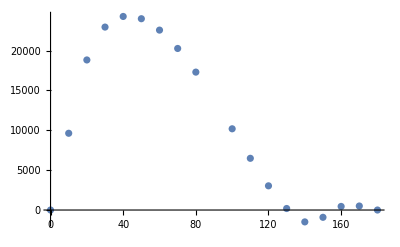

```mathematica
ListPlot[Table[{θ,Salmon[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]},{θ,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]
```

### Visualizing Boat Shape

```mathematica
RegionPlot3D[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x, -10, 10},{y, 0, 20},{z, 0, 20}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

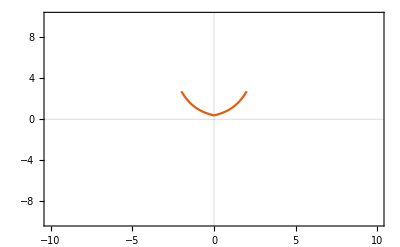

```mathematica
Show[Plot[(1)*Abs[Exp[x-1]], {x,0,2},PlotRange->{{-10,10},{-10,10}}, PlotTheme->"Scientific"],Plot[(1)*Abs[Exp[-x-1]], {x,-2,0},PlotRange->{{-10,10},{-10,10}}, PlotTheme->"Scientific"]]
```

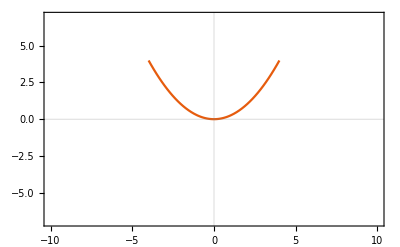

```mathematica
Plot[(1/4)*x^2, {x,-4,4},PlotRange->{{-10,10},{-7,7}}, PlotTheme->"Scientific"]
```

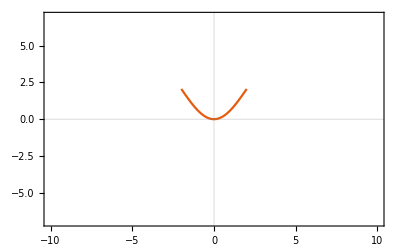

```mathematica
Plot[-2*Cos[x*(4/5)]+2, {x,-2,2},PlotRange->{{-10,10},{-7,7}}, PlotTheme->"Scientific"]
```